3.3×10^-10

3.×10^-11

1.7×10^-11

0.00729753

0.1101

0.09207

5.×10^-8

1.25959×10^-6

0.000022

0.00026197

5.×10^-7

0.134977

1.8×10^-7

0.139571

0.000017

0.547882

0.00023

0.775538

0.00013

0.782687

0.000016

1.01947

0.00013

0.00864741

0.0008

0.148687

0.000013

0.00424785

49/50

0.000016

0.493665

0.938272

-Graphics3D-

0.01

0.689416

0.01

0.659903

0.5

41.0696

0.723583

0.1

0.0566196

0.02

0.857405

0.229805

0.442999

0.688311

0.136066

0.0390136

0.20884

0.101804

0.093656

0.00814761

21.1867

28.8815

4.14464×10^-7

1.58747×10^-10

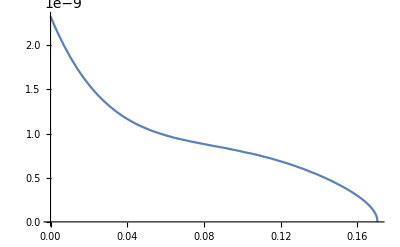

0.0055

3.68×10^-9

1.16×10^-9

0.0375

2.02×10^-9

5.7×10^-10

0.0575

2.22×10^-9

4.8×10^-10

0.0775

2.01×10^-9

4.4×10^-10

0.0975

1.97×10^-9

4.1×10^-10

0.11875

1.77×10^-9

3.6×10^-10

0.15

9.5×10^-10

2.3×10^-10

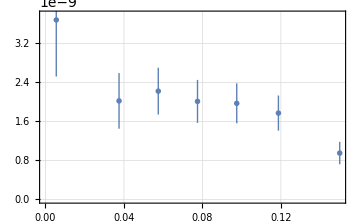

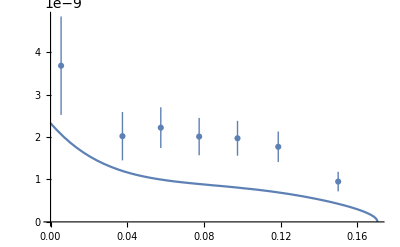

0.0055

1.96×10^-9

9.5452×10^-10

0.0375

1.05×10^-9

5.355×10^-10

0.0575

1.09×10^-9

4.36×10^-10

0.0775

1.22×10^-9

4.27×10^-10

0.0975

1.05×10^-9

2.793×10^-10

0.11875

4.2×10^-10

3.8934×10^-10

0.15

2.8×10^-10

1.9852×10^-10

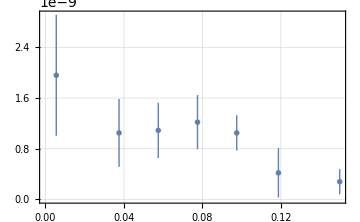

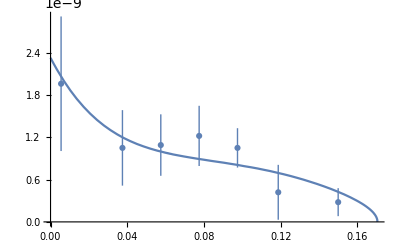

1.58747×10^-10

0.00012603

{{0.0000929293,2.30831},{0.0000949495,2.32627},{0.0000909091,2.34029}}

8.92646×10^-7

3.41899×10^-10

0.000271436

{0.0000929293,MB,3.41899×10^-10,0.000271436}

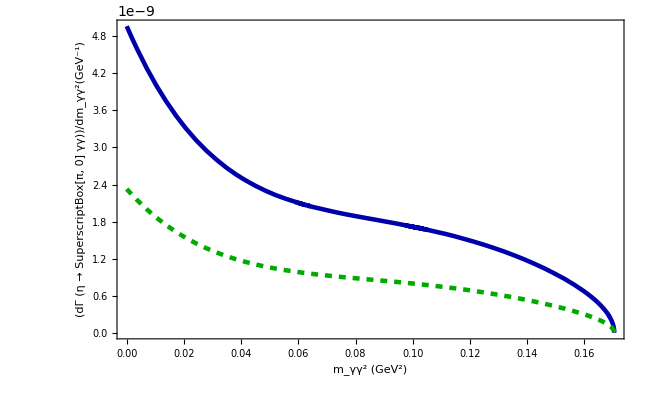

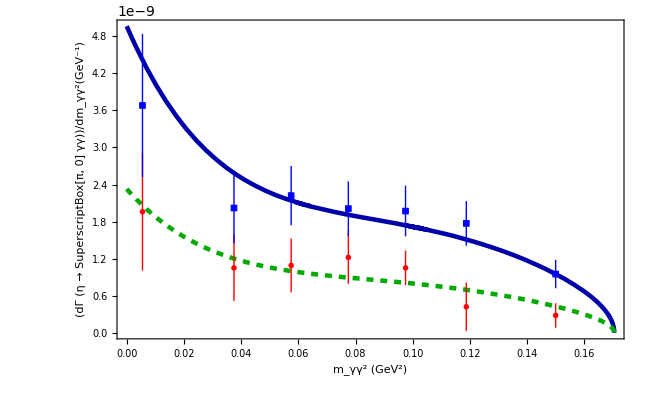

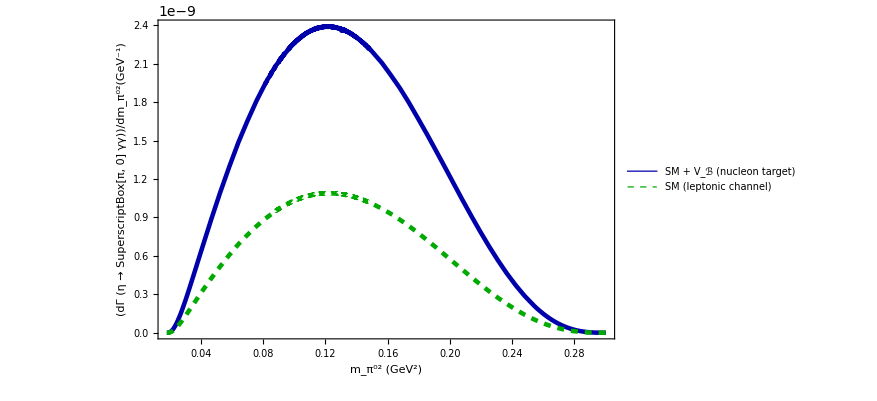

η → π^0γγ: γγ and π^0γ Spectra  with and without V_ℬ (Nucleon Target) | 
-Graphics- | -Graphics-

EtaPi0GammaGamma_1.png

{{0.0000929293,2.30831},{0.0000949495,2.32627},{0.0000909091,2.34029}}

{1.58747×10^-10,0.00012603}

{0.0000929293,MB,3.41899×10^-10,0.000271436}

```mathematica
(*Run 1*)
GenerateValue[M0_,sigma_]:=If[sigma==0,M0,RandomVariate[NormalDistribution[M0,sigma]]]
ΓMAMI=0.33*10^(-9)
ΔΓMAMI=0.03*10^(-9)
Δα=0.000000017*10^(-3)
α=GenerateValue[7.297525664*10^(-3),Δα]
fK =110.10*10^(-3)
fπ =92.07*10^(-3)
ΔΓtotal=0.05*10^(-6)
Γtotal=GenerateValue[1.31*10^(-6),ΔΓtotal]
ΔBR=0.22*10^(-4)
BR=GenerateValue[2.56*10^(-4),ΔBR]
Δmπ=0.0005*10^(-3)
mπ=GenerateValue[134.9768*10^(-3),Δmπ]
ΔmπA=0.00018*10^(-3)
mπA=GenerateValue[139.57039*10^(-3),ΔmπA]
ΔMη=0.017*10^(-3)
Mη = GenerateValue[547.862*10^(-3),ΔMη]
Δmρ=0.23*10^(-3)
mρ=GenerateValue[775.26*10^(-3),Δmρ]
Δmω=0.13*10^(-3)
mω=GenerateValue[782.66*10^(-3),Δmω]
Δmϕ=0.016*10^(-3)
mϕ=GenerateValue[1019.461*10^(-3),Δmϕ]
ΔΓω =0.13*10^(-3)
Γω = GenerateValue[8.68*10^(-3),ΔΓω]
ΔΓρ=0.8*10^(-3)
Γρ = GenerateValue[149.1*10^(-3),ΔΓρ]
ΔΓϕ=0.013*10^(-3)
Γϕ = GenerateValue[4.249*10^(-3),ΔΓϕ]
maZero = 980*10^(-3)
ΔmKP=0.016*10^(-3)
mKP=GenerateValue[493.677*10^(-3),ΔmKP]
mN=GenerateValue[938.27208816*10^(-3),0.00000029*10^(-3)]
ΓρEff[t_] :=Γρ*((-4 mπA^2+t)/(-4 mπA^2+mρ^2))^(3/2) *HeavisideTheta[-4 mπA^2+t]
m232MAX[m132_] := ((Mη^2+mπ^2)^2)/(4 m132)-(-(-m132+Mη^2)/(2 √m132)+√(-mπ^2+((m132+mπ^2)^2)/(4 m132)))^2
m232MIN[m132_] := ((Mη^2+mπ^2)^2)/(4 m132)-((-m132+Mη^2)/(2 √m132)+√(-mπ^2+((m132+mπ^2)^2)/(4 m132)))^2
Constraint[m132_, m232_]:=HeavisideTheta[m232MAX[m132]-m232]*HeavisideTheta[m232-m232MIN[m132]]
Plot3D[Constraint[m132, m232], {m132, mπ^2, Mη^2},{m232, mπ^2, Mη^2}, PlotRange->All]
Δg=0.01
g =GenerateValue[0.70,Δg]
ΔzSmBm=0.01
zSmBm =GenerateValue[0.65,ΔzSmBm]
ΔϕP=0.5
GenerateValue[41.4,ΔϕP]
ϕP = (GenerateValue[41.4,ΔϕP])Degree
ΔϕV=0.1
ϕV =(GenerateValue[3.3,ΔϕV])Degree
ΔzNS=0.02
zNS = GenerateValue[0.83,ΔzNS]
gρπγ = g/3
gρηγ = g*zNS*Cos[ϕP]
gωπγ = g*Cos[ϕV]
gωηγ =g/3*(zNS*Cos[ϕP]*Cos[ϕV]-2*zSmBm*Sin[ϕP]*Sin[ϕV])
gϕπγ = g*Sin[ϕV]
gϕηγ =g/3*(zNS*Cos[ϕP]*Sin[ϕV]+2*zSmBm*Sin[ϕP]*Cos[ϕV])
cρ = gρπγ*gρηγ
cω = gωπγ*gωηγ
cϕ = gϕπγ*gϕηγ
Bq2Bq2p[m132_,m232_]:=1/8 (m132^2+Mη^4) (-m132-m232+Mη^2+mπ^2)^2 +1/8 (-m132+Mη^2) (-m232+Mη^2) (m132 m232+Mη^2 (m132+m232-Mη^2-2 mπ^2))
Bq1Bq1[m132_,m232_]:=1/8 (m232^2+Mη^4) (-m132-m232+Mη^2+mπ^2)^2 +1/8 (-m132+Mη^2) (-m232+Mη^2) (m132 m232+Mη^2 (m132+m232-Mη^2-2 mπ^2))
Bq2Bq1[m132_,m232_]:=1/8 (m132*m232+Mη^4) (-m132-m232+Mη^2+mπ^2)^2 +1/8 (-m132+Mη^2) (-m232+Mη^2) (m132 m232+Mη^2 (m132+m232-Mη^2-2 mπ^2))
BWt[m132_,m232_] := Abs[cρ/(-m132+mρ^2-ⅈ mρ *ΓρEff[m132])+cϕ/(-m132+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m132+mω^2-ⅈ mω Γω)]^2
BWu[m132_,m232_] := Abs[cρ/(-m232+mρ^2-ⅈ mρ *ΓρEff[m232])+cϕ/(-m232+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m232+mω^2-ⅈ mω Γω)]^2
BWtu[m132_,m232_] :=Re[(cρ/(-m132+mρ^2-ⅈ mρ*ΓρEff[m132])+cϕ/(-m132+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m132+mω^2-ⅈ mω Γω))*(cρ/(-m232+mρ^2+ⅈ mρ*ΓρEff[m232])+cϕ/(-m232+mϕ^2+ⅈ mϕ Γϕ)+cω/(-m232+mω^2+ⅈ mω Γω))]
MatrixVMD[m132_,m232_] := (Bq2Bq2p[m132,m232]*BWt[m132,m232]+2*Bq2Bq1[m132,m232]*BWtu[m132,m232] +Bq2Bq1[m132,m232]*BWu[m132,m232])*Constraint[m132, m232]
βPlusπη[s_]:=√(1-(Mη+mπ)^2/s)
βMinusπη[s_]:=√(1-(Mη-mπ)^2/s)
βBarPlusπη[s_]:=√(-1+(Mη+mπ)^2/s)
βBarMinusπη[s_]:=√(-1+(-Mη+mπ)^2/s)
βK[s_]:=√(1-(4*mKP^2)/s)
βKbar[s_]:=√((4*mKP^2)/s-1)
θπη[s_]:= HeavisideTheta[-(Mη+mπ)^2+s]
Barθπη[s_]:= HeavisideTheta[(Mη+mπ)^2-s]*HeavisideTheta[-(-Mη+mπ)^2+s]
BarBarθπη[s_]:= HeavisideTheta[(-Mη+mπ)^2-s]
θK[s_]:= HeavisideTheta[-4*mKP^2+s]
θKbar[s_]:= HeavisideTheta[4*mKP^2-s]
ga0KKbarSq=((-maZero^2+mKP^2)^2)/(2 fK^2)
ga0πηSq=((-maZero^2+Mη^2)^2 Cos[ϕP]^2)/fπ^2
R1[s_]:=ga0KKbarSq/(16 π^2)*(2-Log[(1+βK[s])/(1-βK[s])] *βK[s]* θK[s]-2 ArcTan[1/βKbar[s]]* βKbar[s]* θKbar[s])
R2[s_]:=ga0πηSq/(16 π^2)*(2-((Mη^2-mπ^2) *Log[Mη/mπ])/s-Log[(βMinusπη[s]+βPlusπη[s])/(βMinusπη[s]-βPlusπη[s])]* βMinusπη[s]* βPlusπη[s]* θπη[s])
R3[s_]:=ga0πηSq/(16 π^2)*(BarBarθπη[s]*Log[(βBarMinusπη[s]+βBarPlusπη[s])/(-βBarMinusπη[s]+βBarPlusπη[s])]*βBarMinusπη[s]*βBarPlusπη[s]-2*ArcTan[βMinusπη[s]/βBarPlusπη[s]]*Barθπη[s]*βBarPlusπη[s]*βMinusπη[s])
R[s_]:=R1[s]+R2[s]+R3[s]
ImaginaryPart[s_]:=-(ga0KKbarSq* βK[s]* θK[s])/(16 π)-1/(16 π)ga0πηSq* βPlusπη[s]* βMinusπη[s]*θπη[s]
Da0[s_]:=-maZero^2+s+R[s]-R[maZero^2]+I*ImaginaryPart[s]
ALSM[s_]:=1/(2*fK*fπ)*((-Mη^2+s)*((-maZero^2+mKP^2)/Da0[s])*Cos[ϕP]+1/6 ((5 Mη^2+mπ^2-3 s)*Cos[ϕP]-√2*(4 mKP^2+Mη^2+mπ^2-3 s)*Sin[ϕP]))
f[z_]:=1/4* HeavisideTheta[1/4-z] *(-ⅈ π+Log[(1+√(1-4 z))/(1-√(1-4 z))])^2-ArcSin[1/(2 √z)]^2 HeavisideTheta[-1/4+z]
L[z_]:=-1/(2 z)-(2 f[1/z])/z^2
Int1VMDLSM[m132_,m232_]:=(2 α)/(π*mKP^2)*L[(-m132-m232+Mη^2+mπ^2)/mKP^2]*ALSM[-m132-m232+Mη^2+mπ^2]
Int2VMDLSM[m132_,m232_]:=-Conjugate[1/4 (-m132-m232+Mη^2+mπ^2)^2*(m132*(cρ/(-m132+mρ^2-ⅈ mρ *ΓρEff[m132])+cϕ/(-m132+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m132+mω^2-ⅈ mω Γω))+m232*(cρ/(-m232+mρ^2-ⅈ mρ *ΓρEff[m232])+cϕ/(-m232+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m232+mω^2-ⅈ mω Γω)))]
Interference[m132_,m232_]:=2*Re[Int1VMDLSM[m132,m232]*Int2VMDLSM[m132,m232]]*Constraint[m132, m232]
LSM[m132_,m232_]:=2/π^2(-m132-m232+Mη^2+mπ^2)^2*Abs[1/mKP^2 α ALSM[-m132-m232+Mη^2+mπ^2]* L[(-m132-m232+Mη^2+mπ^2)/mKP^2]]^2*Constraint[m132, m232]
IntegrandSM = NIntegrate[MatrixVMD[m132,m232]+Interference[m132,m232]+LSM[m132,m232], {m132, mπ^2, Mη^2}, {m232, mπ^2, Mη^2} ,AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
Width = (1/2)*1/(256 Mη^3 π^3)*(IntegrandSM)
γγSpectrum[m122_] := NIntegrate[(1/2)*1/(256 Mη^3 π^3)*(MatrixVMD[m132,Mη^2+mπ^2 - m132 - m122]+Interference[m132,Mη^2+mπ^2 - m132 - m122]+LSM[m132,Mη^2+mπ^2 - m132 - m122])*Constraint[m132, Mη^2+mπ^2 - m132 - m122], {m132, mπ^2,Mη^2},AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
pTheory= Plot[γγSpectrum[m122],{m122, 0, (Mη-mπ)^2} , MaxRecursion->5]
p1 = 0.0055
v1 = 3.68*10^(-9)
u1 = (1.16)*10^(-9)
p2 = 0.0375
v2 = 2.02*10^(-9)
u2 = (0.57)*10^(-9)
p3 = 0.0575
v3 = 2.22*10^(-9)
u3 = (0.48)*10^(-9)
p4 = 0.0775
v4 = 2.01*10^(-9)
u4 = (0.44)*10^(-9)
p5 =0.0975
v5=1.97*10^(-9)
u5 = (0.41)*10^(-9)
p6 = 0.11875
v6 =1.77*10^(-9)
u6=(0.36)*10^(-9)
p7 =0.15
v7 =0.95*10^(-9)
u7  = (0.23)*10^(-9)
pExpMAMI=ListPlot[{{Around[p1,0],Around[v1,u1]},
{Around[p2,0],Around[v2,u2]},
{Around[p3,0],Around[v3,u3]},
{Around[p4,0],Around[v4, u4]},
{Around[p5,0],Around[v5,u5]},
{Around[p6,0],Around[v6,u6]},
{Around[p7,0],Around[v7,u7]}},Sequence[PlotTheme->"Detailed",ImageSize->Medium]]
Show[pTheory, pExpMAMI, PlotRange->All]
p1KLOE= (0+0.011)/2
v1KLOE = 1.96*10^(-9)
u1KLOE = v1KLOE*48.7/100
p2KLOE= (0.0275+0.0475)/2
v2KLOE = 1.05*10^(-9)
u2KLOE = v2KLOE*51.0/100
p3KLOE= (0.0475+0.0675)/2
v3KLOE = 1.09*10^(-9)
u3KLOE = v3KLOE*40.0/100
p4KLOE= (0.0675+0.0875)/2
v4KLOE = 1.22*10^(-9)
u4KLOE = v4KLOE*35.0/100
p5KLOE= (0.0875+0.1075)/2
v5KLOE = 1.05*10^(-9)
u5KLOE = v5KLOE*26.6/100
p6KLOE= (0.1075+0.13)/2
v6KLOE = 0.42*10^(-9)
u6KLOE = v6KLOE*92.7/100
p7KLOE= (0.13+0.17)/2
v7KLOE = 0.28*10^(-9)
u7KLOE = v7KLOE*70.9/100
pExpKLOE=ListPlot[{{Around[p1KLOE,0],Around[v1KLOE,u1KLOE]},
{Around[p2KLOE,0],Around[v2KLOE,u2KLOE]},
{Around[p3KLOE,0],Around[v3KLOE,u3KLOE]},
{Around[p4KLOE,0],Around[v4KLOE, u4KLOE]},
{Around[p5KLOE,0],Around[v5KLOE,u5KLOE]},
{Around[p6KLOE,0],Around[v6KLOE,u6KLOE]},
{Around[p7KLOE,0],Around[v7KLOE,u7KLOE]}},Sequence[PlotTheme->"Detailed",ImageSize->Medium]]
Show[pTheory, pExpKLOE, PlotRange->All]
Width
BranchingTheory=Width/Γtotal
BWtDARK[m132_,m232_,Yukawa2Cs2Ms6MB2_] := Abs[cρ/(-m132+mρ^2-ⅈ mρ *ΓρEff[m132])+cϕ/(-m132+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m132+mω^2-ⅈ mω Γω)+Yukawa2Cs2Ms6MB2*(4*64 mN^6)/α*cω]^2
BWuDARK[m132_,m232_,Yukawa2Cs2Ms6MB2_] := Abs[cρ/(-m232+mρ^2-ⅈ mρ *ΓρEff[m232])+cϕ/(-m232+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m232+mω^2-ⅈ mω Γω)+Yukawa2Cs2Ms6MB2*(4*64 mN^6)/α*cω]^2
BWtuDARK[m132_,m232_,Yukawa2Cs2Ms6MB2_]:=Re[(cρ/(-m132+mρ^2-ⅈ mρ*ΓρEff[m132])+cϕ/(-m132+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m132+mω^2-ⅈ mω Γω)+Yukawa2Cs2Ms6MB2*(4*64 mN^6)/α*cω)*(cρ/(-m232+mρ^2+ⅈ mρ*ΓρEff[m232])+cϕ/(-m232+mϕ^2+ⅈ mϕ Γϕ)+cω/(-m232+mω^2+ⅈ mω Γω)+Yukawa2Cs2Ms6MB2*(4*64 mN^6)/α*cω)]
MatrixVMDDARK[m132_,m232_,Yukawa2Cs2Ms6MB2_] := (Bq2Bq2p[m132,m232]*BWtDARK[m132,m232,Yukawa2Cs2Ms6MB2]+2*Bq2Bq1[m132,m232]*BWtuDARK[m132,m232,Yukawa2Cs2Ms6MB2] +Bq2Bq1[m132,m232]*BWuDARK[m132,m232,Yukawa2Cs2Ms6MB2])*Constraint[m132, m232]
Int1VMDLSMDARK[m132_,m232_,Yukawa2Cs2Ms6MB2_]:=(2 α)/(π*mKP^2)*L[(-m132-m232+Mη^2+mπ^2)/mKP^2]*ALSM[-m132-m232+Mη^2+mπ^2]
Int2VMDLSMDARK[m132_,m232_,Yukawa2Cs2Ms6MB2_]:=-Conjugate[1/4 (-m132-m232+Mη^2+mπ^2)^2*(m132*(cρ/(-m132+mρ^2-ⅈ mρ *ΓρEff[m132])+cϕ/(-m132+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m132+mω^2-ⅈ mω Γω)+Yukawa2Cs2Ms6MB2*(4*64 mN^6)/α*cω)+m232*(cρ/(-m232+mρ^2-ⅈ mρ *ΓρEff[m232])+cϕ/(-m232+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m232+mω^2-ⅈ mω Γω)+Yukawa2Cs2Ms6MB2*(4*64 mN^6)/α*cω))]
InterferenceDARK[m132_,m232_,Yukawa2Cs2Ms6MB2_]:=2*Re[Int1VMDLSMDARK[m132,m232,Yukawa2Cs2Ms6MB2]*Int2VMDLSMDARK[m132,m232,Yukawa2Cs2Ms6MB2]]*Constraint[m132, m232]
γγSpectrumDARK[m122_,Yukawa2Cs2Ms6MB2_] := NIntegrate[(1/2)*1/(256 Mη^3 π^3)*(MatrixVMDDARK[m132,Mη^2+mπ^2 - m132 - m122,Yukawa2Cs2Ms6MB2]+InterferenceDARK[m132,Mη^2+mπ^2 - m132 - m122,Yukawa2Cs2Ms6MB2]+LSM[m132,Mη^2+mπ^2 - m132 - m122])*Constraint[m132, Mη^2+mπ^2 - m132 - m122], {m132, mπ^2,Mη^2},AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->50]
Loss[x_]:=1/u1^2(γγSpectrumDARK[p1,x]- v1)^2+1/u2^2(γγSpectrumDARK[p2,x]- v2)^2+1/u3^2(γγSpectrumDARK[p3,x]- v3)^2+1/u4^2(γγSpectrumDARK[p4,x]- v4)^2+1/u5^2(γγSpectrumDARK[p5,x]- v5)^2+1/u6^2(γγSpectrumDARK[p6,x]- v6)^2+1/u7^2(γγSpectrumDARK[p7,x]- v7)^2
(*1) Grid setup*)nx=100;
xMin=0;
xMax=0.2*10^(-3);
dx=(xMax-xMin)/(nx-1);
(*2) Initialize “top-3 so far” list and a counter for the progress bar*)
bestList={};(*will hold up to 3 {x,loss} pairs*)count=0;
(*3) Brute-force loop over x only*)
Monitor[For[i=0,i<nx,i++,x=xMin+i*dx;
loss=Loss[x];(*here Loss should depend only on x (and any fixed other args)*)count++;
(*insert and keep only best 3 by ascending loss*)bestList=Append[bestList,{x,loss}];
bestList=SortBy[bestList,Last];
bestList=Take[bestList,UpTo[3]];],ProgressIndicator[Dynamic[count],{0,nx}]];
(*4) Show the three best results*)
bestList
(*If you just want the very best x and its loss:*)
BestYukawa2Cs2Ms6MB2=bestList[[1,1]];
BestLoss=bestList[[1,2]];
IntegrandDark = NIntegrate[MatrixVMDDARK[m132,m232,BestYukawa2Cs2Ms6MB2]+InterferenceDARK[m132,m232,BestYukawa2Cs2Ms6MB2]+LSM[m132,m232], {m132, mπ^2, Mη^2}, {m232, mπ^2, Mη^2} ,AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
WidthDark = (1/2)*1/(256 Mη^3 π^3)*(IntegrandDark)
BranchingDark=WidthDark/Γtotal
Output={BestYukawa2Cs2Ms6MB2,MB,WidthDark,BranchingDark}
SummaryTheory= Plot[{{γγSpectrumDARK[m122,BestYukawa2Cs2Ms6MB2]},{γγSpectrum[m122]}},{m122, 0, (Mη-mπ)^2}, PlotRange->All,PlotStyle->{Directive[Darker[Blue], Thickness[0.005]],Directive[Darker[Green], Thickness[0.005], Dashed]}, Frame->True, FrameStyle->Directive[Black,Thick], LabelStyle->Large,PlotLegends-> None, Frame->True, FrameStyle->Directive[Black,Thick], LabelStyle->Large,PlotLegends-> LineLegend[{"SM + V_ℬ (nucleon target)","SM (leptonic channel)"}, LegendFunction->Framed],PlotStyle->{Directive[Darker[Green], Thickness[0.007]]},FrameLabel->{"m_γγ^2 (GeV^2)","(dΓ (η →  SuperscriptBox[π, 0] γγ))/dm_γγ^2(GeV^-1)"},  LabelStyle->{FontWeight->"Bold", FontSize->25}, ImageSize->650]
pExpKLOE=ListPlot[{{Around[p1KLOE,0],Around[v1KLOE,u1KLOE]},{Around[p2KLOE,0],Around[v2KLOE,u2KLOE]},{Around[p3KLOE,0],Around[v3KLOE,u3KLOE]},{Around[p4KLOE,0],Around[v4KLOE,u4KLOE]},{Around[p5KLOE,0],Around[v5KLOE,u5KLOE]},{Around[p6KLOE,0],Around[v6KLOE,u6KLOE]},{Around[p7KLOE,0],Around[v7KLOE,u7KLOE]}},PlotStyle->{Red,PointSize[Large]},PlotMarkers->{Graphics[{Red,Disk[]}],0.02},Joined->False,PlotTheme->"Detailed",ImageSize->Medium];
pExpMAMI=ListPlot[{{Around[p1,0],Around[v1,u1]},{Around[p2,0],Around[v2,u2]},{Around[p3,0],Around[v3,u3]},{Around[p4,0],Around[v4,u4]},{Around[p5,0],Around[v5,u5]},{Around[p6,0],Around[v6,u6]},{Around[p7,0],Around[v7,u7]}},PlotStyle->{Blue,PointSize[Large]},PlotMarkers->{Graphics[{Blue,EdgeForm[Thick],Rectangle[{-.02,-.02},{.02,.02}]}],0.02},Joined->False,PlotTheme->"Detailed",ImageSize->Large];
Part1 = Show[SummaryTheory,pExpKLOE,pExpMAMI]
πγIntegral[m132_] := NIntegrate[MatrixVMD[m132,m232]+Interference[m132,m232]+LSM[m132,m232], {m232, mπ^2, Mη^2} ,AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
πγSpectrum[m132_]  := (1/2)*1/(256 Mη^3 π^3)*(πγIntegral[m132])
πγIntegrandDark[m132_,Yukawa2Cs2Ms6MB2_]:= NIntegrate[MatrixVMDDARK[m132,m232,Yukawa2Cs2Ms6MB2]+InterferenceDARK[m132,m232,Yukawa2Cs2Ms6MB2]+LSM[m132,m232], {m232, mπ^2, Mη^2} ,AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
πγSpectrumDark[m132_,Yukawa2Cs2Ms6MB2_]  := (1/2)*1/(256 Mη^3 π^3)*(πγIntegrandDark[m132,Yukawa2Cs2Ms6MB2])
Part2 = Plot[{{πγSpectrumDark[m132,BestYukawa2Cs2Ms6MB2]},{πγSpectrum[m132]}},{m132, (mπ)^2, (Mη)^2}, PlotRange->All,PlotStyle->{Directive[Darker[Blue], Thickness[0.005]],Directive[Darker[Green], Thickness[0.005], Dashed],Directive[Darker[Black],Thickness[0.005]],Directive[Darker[Blue],Dotted],Directive[Darker[Pink], Dashed,Thickness[0.005]],Directive[Darker[Red], Thickness[0.005]]}, Frame->True, FrameStyle->Directive[Black,Thick], LabelStyle->Large,PlotLegends-> LineLegend[{"SM + V_ℬ (nucleon target)","SM (leptonic channel)"}, LegendFunction->Framed], Frame->True, FrameStyle->Directive[Black,Thick], LabelStyle->Large, PlotStyle->{Directive[Darker[Green], Thickness[0.007]]},FrameLabel->{"m_(π^0)^2 (GeV^2)","(dΓ (η →  SuperscriptBox[π, 0] γγ))/(dm_(π^0)^2)(GeV^-1)"},  LabelStyle->{FontWeight->"Bold", FontSize->25}, ImageSize->650,Axes->False]
title=Panel[Style["η → π^0γγ: γγ and π^0γ Spectra  with and without V_ℬ (Nucleon Target)",White,40],ImageSize->1500,Background->Blue,Alignment->Center];
DependenceVariation=Deploy@Grid[{{title,SpanFromLeft},{Part1,Part2}},Dividers->Gray,Spacings->{0,0}]
Export["EtaPi0GammaGamma_1.png",DependenceVariation,ImageSize->5000]
bestList
SMOutpt={Width,BranchingTheory}
Output
```